```mathematica
Map[#->Red&,Table[allGraphs5[k,"colofour"],{k,{alfa1Key}}]]
```

{v13x24x5→RGBColor[1, 0, 0]}

```mathematica
Graph[FormulaGraphReverse2[Map[allGraphs5[#,"colofour"]&,Select[allGraphs5AtomKeys,allGraphs5[#,"atleast"]==0&]]], GraphHighlight->Table[allGraphs5[k,"colofour"],{k,Join[alfa1s,quads]}], GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Graph[FormulaGraphReverse2[Map[allGraphs5[#,"colofour"]&,Select[allGraphs5AtomKeys,!MemberQ[quads,#]&&allGraphs5[#,"atleast"]==0&]]], GraphHighlight->Table[allGraphs5[k,"colofour"],{k,Join[alfa1s,quads]}], GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Table[ShowGraph5Least[k],{k,allGraphs5AtomKeys}]
```

{-Graphics-295240,-Graphics-295250,-Graphics-295270,-Graphics-295330,-Graphics-295371,-Graphics-295510,-Graphics-295600,-Graphics-296050,-Graphics-296080,-Graphics-296330,-Graphics-297670,-Graphics-297681,-Graphics-297970,-Graphics-298571,-Graphics-298881,-Graphics-302530,-Graphics-302621,-Graphics-303340,-Graphics-304961,-Graphics-305861,-Graphics-317110,-Graphics-317140,-Graphics-317380,-Graphics-319540,-Graphics-319840,-Graphics-324411,-Graphics-326841,-Graphics-360850,-Graphics-360860,-Graphics-361120,-Graphics-361660,-Graphics-361940,-Graphics-368170,-Graphics-368980,-Graphics-382810,-Graphics-383080,-Graphics-390141,-Graphics-492070,-Graphics-492081,-Graphics-492100,-Graphics-492161,-Graphics-492201,-Graphics-499631,-Graphics-499721,-Graphics-514750,-Graphics-514780,-Graphics-522321,-Graphics-560111,-Graphics-560121,-Graphics-567701,-Graphics-582881,-Graphics-590481}

```mathematica
Graph[FormulaGraphReverse2[Map[allGraphs6[#,"colofour"]&,Select[allGraphs5AtomKeys,!MemberQ[quads,#]&&allGraphs6[#,"comp"]=!=Greater&]]], GraphHighlight->Table[allGraphs6[k,"colofour"],{k,Join[alfa1s,quads]}], GraphHighlightStyle->"Thick"]
```

-Graphics-

```mathematica
Table[allGraphs5[k,"comp"],{k,allGraphs5AtomKeys}]//Tally//Sort
```

{{Equal,1},{Greater,21},{GreaterEqual,30}}

```mathematica
Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]=!=Greater&]
```

{7174453,7174454,7174456,7174462,7174466,7174480,7174489,7174534,7174537,7174562,7174696,7174697,7174726,7174786,7175182,7175191,7175263,7175425,7175515,7176640,7176643,7176667,7176883,7176913,7177370,7177613,7181014,7181015,7181041,7181095,7181123,7181746,7181827,7183210,7183237,7183943,7194136,7194137,7194139,7194145,7194892,7194901,7196404,7196407,7197161,7200940,7201699,7233502,7233511,7233583,7233745,7235689,7235932,7240063,7240144,7242259,7253185,7255453,7351600,7351603,7351627,7351843,7351873,7352329,7352572,7358161,7358188,7358893,7371283,7371286,7372039,7378087,7378846,7410650,7417211,7705894,7705895,7705921,7705975,7706003,7706623,7706704,7708081,7708108,7708811,7725577,7725578,7726333,7727845,7728602,7764946,7765027,7767133,7784629,7786897,7883050,7883077,7883779,7902733,7903489,8768776,8768777,8768779,8768785,8768789,8769505,8769514,8770963,8770966,8771693,8775337,8775338,8776069,8777533,8778266,8827852,8827861,8830039,8834413,8836609,8946004,8946007,8946733,8952565,8953297,9005081,9011642,9300460,9300461,9301189,9302647,9303377,9359539,9361726,9477697,9478426,11957422,11957423,11957425,11957431,11957449,11957458,11957503,11957506,11957531,11957665,11957695,12017200,12017281,12136756,12136759,12136783,12136999,12137029,12495424,12495425,12495451,12495505,12495533,12555205,12555286,12674767,12674794,13571428,13571431,13750843,13750846}

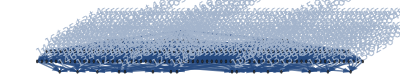

```mathematica
Map[allGraphs6[#,"colofour"]&,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]=!=Greater&]]//FormulaGraphReverse2
```

```mathematica
Map[Length[SymbolToSets[allGraphs6[#,"colofour"]]]&,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]=!=Greater&]]//Tally//Sort
```

{{2,16},{3,70},{4,65},{5,15},{6,1}}

```mathematica
Map[Length[SymbolToSets[allGraphs5[#,"colofour"]]]&,Select[allGraphs5AtomKeys,allGraphs5[#,"comp"]=!=Greater&]]//Tally//Sort
```

{{2,5},{3,15},{4,10},{5,1}}

```mathematica
Map[Length[SymbolToSets[allGraphs6[#,"colofour"]]]&,Select[allGraphs6AtomKeys,allGraphs6[#,"comp"]===Equal&]]//Tally//Sort
```

{{5,15},{6,1}}